```mathematica
beam intensity  4 sigma diameter = 1/e^2 intensity diameter
```

```mathematica
z=2.5+Join[Range[0,7],{12,16}];
z=z 25.4 mm;
wx={790,800,810,815,830,850,860,880,1040,1300}um/2;
wx=Thread[{z,wx}];
wy={730,730,740,740,750,755,760,780,895,1120}um/2;
wy=Thread[{z,wy}];
```

w0x [um] | zRx [mm] | zR_exp [mm]
394.566 | 292.202 | 501.118

w0y [um] | zRy [mm] | zR_exp [mm]
357.154 | 291.193 | 410.593

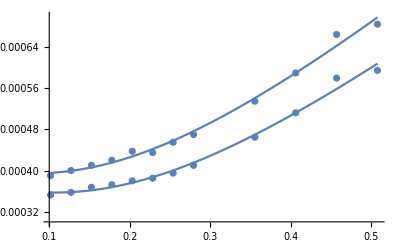

```mathematica
z=4+Join[Range[0,7],{12,10,14,16}];
z=z 25.4 mm;
wx={780, 800, 820, 840,875,870, 910, 940, 1180, 1070, 1330, 1370}um/2;
wx=Thread[{z,wx}];
wy={705, 715, 735,745,760,770,790,820,1025,930,1160,1190}um/2;
wy=Thread[{z,wy}];

mm=10^-3;
um=10^-6;
nm=10^-9;
λ=976nm;

Clear[zR,fn,w0,zz]

(*zR[w0_]:=(π w0^2)/λ;*)

fn=w0 √(1+((zz-z0)/zR)^2);
wxfit=FindFit[wx,fn,{{w0,200um},{z0,-25mm},{zR,250mm}},zz];
wyfit=FindFit[wy,fn,{{w0,200um},{z0,-25mm},{zR,250mm}},zz];

wxplots=Show[{
Plot[fn
/.wxfit
,{zz,wx[[1,1]],wx[[-1,1]]},PlotRange->{All,{300um,700um}}],
ListPlot[wx]
}];

wyplots=Show[{
Plot[fn
/.wyfit
,{zz,wy[[1,1]],wy[[-1,1]]},PlotRange->{All,{300um,700um}}],
ListPlot[wy]
}];

{{"w0x [um]","zRx [mm]","zR_exp [mm]"},{w0/um,zR/mm,(π w0^2)/λ/mm}/.wxfit}//TableForm
{{"w0y [um]","zRy [mm]","zR_exp [mm]"},{w0/um,zR/mm,(π w0^2)/λ/mm}/.wyfit}//TableForm

Show[{{wxplots,wyplots}}]
```

## move lens slightly further.

w0x [um] | zRx [mm] | zR_exp [mm]
394.566 | 292.202 | 501.118

w0y [um] | zRy [mm] | zR_exp [mm]
357.154 | 291.193 | 410.593

-Graphics-

```mathematica
wxfit
wyfit
```

{w0→0.000394566,z0→0.0814338,zR→0.292202}

{w0→0.000357154,z0→0.106741,zR→0.291193}

## original

w0x [um] | zRx [mm] | zR_exp [mm]
400.622 | 297.362 | 516.618

w0y [um] | zRy [mm] | zR_exp [mm]
365.403 | 307.047 | 429.777

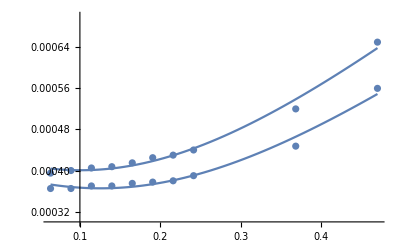

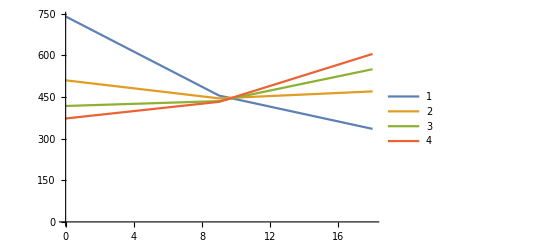

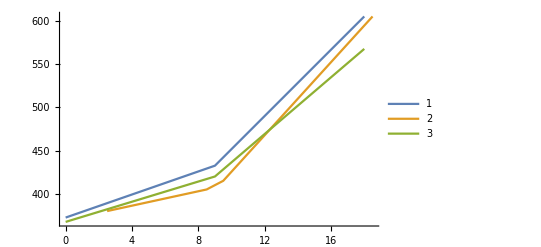

```mathematica
z={0,9,18};
w1={1480,910,670}/2;(*Z0=400+250mm*)
w2={1020,890,940}/2;(*Z0-3 in*)
w3={835,870,1100}/2;(*Z0-5 in*)
w4={745,865,1210}/2;(*Z0-6 in ~ original position*)

dats=Thread[{z,#}]&/@{w1,w2,w3,w4};

z=2.5+Join[Range[0,7],{12,16}];
wx={790,800,810,815,830,850,860,880,1040,1300}/2;
wy={730,730,740,740,750,755,760,780,895,1120}/2;
wAve=(wx+wy)/2;
w5=Thread[{z,wAve}];
w5=Cases[w5,x_/;MemberQ[{8.5,9.5,2.5,18.5},x[[1]]]];

z={0,9,18};
w6=Thread[{z,{735,840,1135}/2}];
dats=Join[dats,{w5,w6}];

ListPlot[dats[[;;-3]],Joined->True,PlotLegends->Automatic]

ListPlot[dats[[-3;;]],Joined->True,PlotLegends->Automatic]
```